### 核関数の平滑化距離の変化の影響を確認する

```mathematica
ClearAll["Global`*"];
```

#### 関数の定義 （設定）

```mathematica
wBspline5[r_,h_]:=Module[{a=2187/(40*Pi),oneThird=1/3,twoThirds=2/3,q=r/h,c},c=a/h^3;
If[q>1,0,If[q<oneThird,(Power[1-q,5]-6*Power[twoThirds-q,5]+15*Power[oneThird-q,5])*c,If[q<twoThirds,(Power[1-q,5]-6*Power[twoThirds-q,5])*c,(Power[1-q,5])*c]]]]

gradWBspline5[xi_List,xj_List,h_]:=Module[{a=2187/(40*Pi),oneThird=1/3,twoThirds=2/3,r,q,gradQ,c,zeros={0.,0.,0.}},r=Norm[xi-xj];
q=r/h;
gradQ=(xi-xj)/(r*h);
c=a/h^4;
If[q>1||q==0,zeros,If[q<oneThird,gradQ*(-5*(1-q)^4+30*(twoThirds-q)^4-75*(oneThird-q)^4)*c,If[q<twoThirds,gradQ*(-5*(1-q)^4+30*(twoThirds-q)^4)*c,gradQ*(-5*(1-q)^4)*c]]]*h
]
```

```mathematica
wBspline3[r_,h_]:=Module[{q=r/h},Which[q>1,0,q<1/2,8*(1-6*q^2+6*q^3)/(Pi*h^3),True,8*2*(1-q)^3/(Pi*h^3)]]

gradWBspline3[xi_List,xj_List,h_]:=Module[{r=Norm[xi-xj],q,gradQ,dinom},q=r/h;
gradQ=(xi-xj)/(r*h);
dinom=Pi*h^4*r;
Which[q>1||dinom<10^-10,{0.,0.,0.},q<1/2,(xi-xj)*(-96+144*q)*q/dinom,True,-48*(xi-xj)*(1-q)^2/dinom]]
```

```mathematica
(*Set values*)
radius=2.;

(*center*)
A={0.,0.,0.};

vec=Subdivide[-radius,radius,20];

(*Generate Dot_grad_w_Bspline3_Dot,Dot_grad_w_Bspline5_Dot,w_Bspline3,w_Bspline5 values for different x,y,z and plot*)
z=0;
dataBspline3=Flatten[Table[{x,y,wBspline3[Norm[{x,y,z}-A],radius]},{x,vec},{y,vec}],1];
ListPlot3D[dataBspline3,AxesLabel->{"x","y","w_Bspline3"},PlotRange->All]

dataBspline5=Flatten[Table[{x,y,wBspline5[Norm[{x,y,z}-A],radius]},{x,vec},{y,vec}],1];
ListPlot3D[dataBspline5,AxesLabel->{"x","y","w_Bspline5"},PlotRange->All]
```

-Graphics3D-

-Graphics3D-

```mathematica
(*テスト*)
```

```mathematica
numericalGradWBspline[X_,A_,h_,e_]:=Module[{F,XPlus,XMinus,n=Length[X],numGrad},
F[x_]:=wBspline3[Norm[x-A],h];
numGrad=Table[XPlus=X;
XMinus=X;
XPlus[[i]]+=e;
XMinus[[i]]-=e;
(F[XPlus]-F[XMinus])/(2*e),{i,n}];
numGrad]

X=A+{0.1,0.1,0.1};

radius=2;

Print["Analytical gradient: ",gradWBspline3[X,A,radius]];
Print["Numerical gradient: ",numericalGradWBspline[X,A,radius,10^-6]];
```

Analytical gradient: {-0.0830881,-0.0830881,-0.0830881}

Numerical gradient: {-0.0830881,-0.0830881,-0.0830881}

```mathematica
F[X_]:=wBspline5[Norm[X-A],radius];

deltaX=RandomReal[{-0.01,0.01},Length[X]];
Print["F[X + deltaX]: ",F[X+deltaX]];
Print["F[X]: ",F[X], ", diff = ", F[X+deltaX]-F[X]];
Print["F[X] + grad dt: ",F[X]+gradWBspline3[X,A,radius].deltaX, ", diff = ", F[X+deltaX]-(F[X]+gradWBspline3[X,A,radius].deltaX)];
Print["F[X] + grad dt: ",F[X]+gradWBspline5[X,A,radius].deltaX, ", diff = ", F[X+deltaX]-(F[X]+gradWBspline5[X,A,radius].deltaX)];
```

F[X + deltaX]: 0.555575

F[X]: 0.555723, diff = -0.000148322

F[X] + grad dt: 0.555713, diff = -0.000138474

F[X] + grad dt: 0.555696, diff = -0.000121398

-Graphics3D-

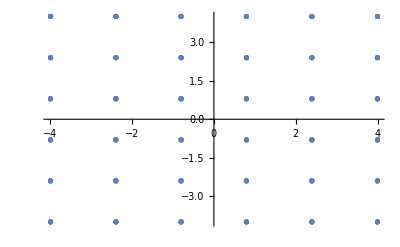

N = 5, sum3 = 0.613022, sum5 = 0.199523

sumGrad3 = {-0.00684749,-0.00684749,-0.00684749}, sumGrad5 = {-0.0104214,-0.0104214,-0.0104214}

sumGrad3 = {-0.00498563,-0.00498563,-0.00498563}, sumGrad5 = {-0.0139867,-0.0139867,-0.0139867}CORRECTED

sumGrad3 = {-0.00498563,-0.00498563,-0.00498563}, sumGrad5 = {-0.0139867,-0.0139867,-0.0139867}CORRECTED

B = (-1.37343 | -9.17984×10^-6 | -9.17984×10^-6
-9.17984×10^-6 | -1.37343 | -9.17984×10^-6
-9.17984×10^-6 | -9.17984×10^-6 | -1.37343), (-0.744942 | -0.0000754429 | -0.0000754429
-0.0000754429 | -0.744942 | -0.0000754429
-0.0000754429 | -0.0000754429 | -0.744942)

B^-1 = (-0.728106 | 4.86655×10^-6 | 4.86655×10^-6
4.86655×10^-6 | -0.728106 | 4.86655×10^-6
4.86655×10^-6 | 4.86655×10^-6 | -0.728106), (-1.34239 | 0.000135934 | 0.000135934
0.000135934 | -1.34239 | 0.000135934
0.000135934 | 0.000135934 | -1.34239)

-Graphics3D-

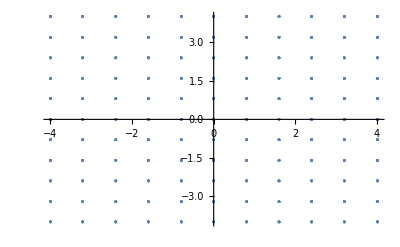

N = 10, sum3 = 0.998916, sum5 = 1.00093

sumGrad3 = {0.00619166,0.00619166,0.00619166}, sumGrad5 = {0.0161701,0.0161701,0.0161701}

sumGrad3 = {0.00629751,0.00629751,0.00629751}, sumGrad5 = {0.0162683,0.0162683,0.0162683}CORRECTED

sumGrad3 = {0.00629751,0.00629751,0.00629751}, sumGrad5 = {0.0162683,0.0162683,0.0162683}CORRECTED

B = (-0.983149 | -0.0000218941 | -0.0000218941
-0.0000218941 | -0.983149 | -0.0000218941
-0.0000218941 | -0.0000218941 | -0.983149), (-0.993858 | -0.000054941 | -0.000054941
-0.000054941 | -0.993858 | -0.000054941
-0.000054941 | -0.000054941 | -0.993858)

B^-1 = (-1.01714 | 0.0000226505 | 0.0000226505
0.0000226505 | -1.01714 | 0.0000226505
0.0000226505 | 0.0000226505 | -1.01714), (-1.00618 | 0.000055619 | 0.000055619
0.000055619 | -1.00618 | 0.000055619
0.000055619 | 0.000055619 | -1.00618)

-Graphics3D-

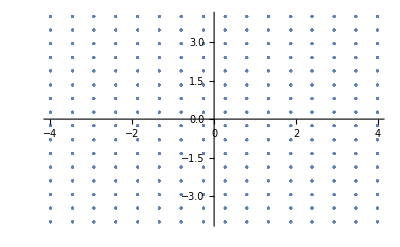

N = 15, sum3 = 0.996621, sum5 = 0.998295

sumGrad3 = {-0.0165892,-0.0165892,-0.0165892}, sumGrad5 = {-0.0234982,-0.0234982,-0.0234982}

sumGrad3 = {-0.0166229,-0.0166229,-0.0166229}, sumGrad5 = {-0.0236474,-0.0236474,-0.0236474}CORRECTED

sumGrad3 = {-0.0166229,-0.0166229,-0.0166229}, sumGrad5 = {-0.0236474,-0.0236474,-0.0236474}CORRECTED

B = (-0.99778 | -0.0000957019 | -0.0000957019
-0.0000957019 | -0.99778 | -0.0000957019
-0.0000957019 | -0.0000957019 | -0.99778), (-0.993445 | -0.000121959 | -0.000121959
-0.000121959 | -0.993445 | -0.000121959
-0.000121959 | -0.000121959 | -0.993445)

B^-1 = (-1.00222 | 0.0000961191 | 0.0000961191
0.0000961191 | -1.00222 | 0.0000961191
0.0000961191 | 0.0000961191 | -1.00222), (-1.0066 | 0.000123558 | 0.000123558
0.000123558 | -1.0066 | 0.000123558
0.000123558 | 0.000123558 | -1.0066)

-Graphics3D-

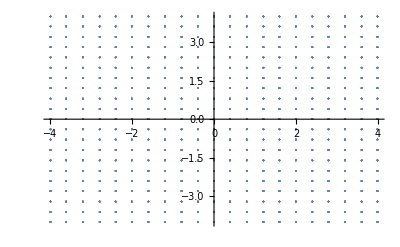

N = 20, sum3 = 1.01846, sum5 = 1.02815

sumGrad3 = {0.00547469,0.00547469,0.00547469}, sumGrad5 = {0.00830172,0.00830172,0.00830172}

sumGrad3 = {0.00543932,0.00543932,0.00543932}, sumGrad5 = {0.00821896,0.00821896,0.00821896}CORRECTED

sumGrad3 = {0.00543932,0.00543932,0.00543932}, sumGrad5 = {0.00821896,0.00821896,0.00821896}CORRECTED

B = (-1.00648 | -0.0000109476 | -0.0000109476
-0.0000109476 | -1.00648 | -0.0000109476
-0.0000109476 | -0.0000109476 | -1.00648), (-1.01004 | -0.0000147853 | -0.0000147853
-0.0000147853 | -1.01004 | -0.0000147853
-0.0000147853 | -0.0000147853 | -1.01004)

B^-1 = (-0.993562 | 0.0000108069 | 0.0000108069
0.0000108069 | -0.993562 | 0.0000108069
0.0000108069 | 0.0000108069 | -0.993562), (-0.990061 | 0.0000144926 | 0.0000144926
0.0000144926 | -0.990061 | 0.0000144926
0.0000144926 | 0.0000144926 | -0.990061)

-Graphics3D-

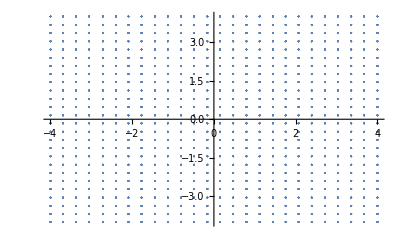

N = 25, sum3 = 1.00318, sum5 = 1.00744

sumGrad3 = {0.00254679,0.00254679,0.00254679}, sumGrad5 = {0.00292743,0.00292743,0.00292743}

sumGrad3 = {0.00255344,0.00255344,0.00255344}, sumGrad5 = {0.00292915,0.00292915,0.00292915}CORRECTED

sumGrad3 = {0.00255344,0.00255344,0.00255344}, sumGrad5 = {0.00292915,0.00292915,0.00292915}CORRECTED

B = (-0.997386 | -3.19186×10^-6 | -3.19186×10^-6
-3.19186×10^-6 | -0.997386 | -3.19186×10^-6
-3.19186×10^-6 | -3.19186×10^-6 | -0.997386), (-0.999409 | -2.00414×10^-6 | -2.00414×10^-6
-2.00414×10^-6 | -0.999409 | -2.00414×10^-6
-2.00414×10^-6 | -2.00414×10^-6 | -0.999409)

B^-1 = (-1.00262 | 3.2086×10^-6 | 3.2086×10^-6
3.2086×10^-6 | -1.00262 | 3.2086×10^-6
3.2086×10^-6 | 3.2086×10^-6 | -1.00262), (-1.00059 | 2.00651×10^-6 | 2.00651×10^-6
2.00651×10^-6 | -1.00059 | 2.00651×10^-6
2.00651×10^-6 | 2.00651×10^-6 | -1.00059)

```mathematica
(*Calculate sum of w_Bspline3 and w_Bspline5 for different N values and print*)
Do[
sum3=0;
sum5=0;
sumGrad3=0;
sumGrad5=0;
sumB3=ConstantArray[0,{3,3}];
sumB5=ConstantArray[0,{3,3}];

{maxx,minx}=2*radius*{1,-1};

range=maxx-minx;
totalVolume=(range)^3;
eachVolume=(range/n)^3;
eps=0.01;
V=(#+RandomReal[{-eps,eps}])&/@Subdivide[minx,maxx,n];
points3D={};
points2D={};

Do[
X={x,y,z};
sum3+=wBspline3[Norm[X-A],radius]*eachVolume;
sum5+=wBspline5[Norm[X-A],radius]*eachVolume;

sumGrad3+=gradWBspline3[X,A,radius]*eachVolume;
sumGrad5+=gradWBspline5[X,A,radius]*eachVolume;

sumB3+=TensorProduct[A-X,gradWBspline3[A,X,radius]]*eachVolume;
sumB5+=TensorProduct[A-X,gradWBspline5[A,X,radius]]*eachVolume;

points3D=Append[points3D,{x,y,z}];
points2D=Append[points2D,{x,y}];
,{x,V},{y,V},{z,V}];


Print[Show[ListPointPlot3D[points3D]]];
Print[Show[ListPlot[points2D]]];

Print["N = ",n,", sum3 = ",sum3,", sum5 = ",sum5];
Print["sumGrad3 = ",sumGrad3,", sumGrad5 = ",sumGrad5];
Print["sumGrad3 = ",sumGrad3.(-Inverse@sumB3),", sumGrad5 = ",sumGrad5.(-Inverse@sumB5), "CORRECTED"];
Print["sumGrad3 = ",(-Inverse@sumB3).sumGrad3,", sumGrad5 = ",(-Inverse@sumB5).sumGrad5, "CORRECTED"];
Print[ "B = ",MatrixForm@sumB3,", ",MatrixForm@sumB5];
Print[ "B^-1 = ",MatrixForm@Inverse@sumB3,", ",MatrixForm@Inverse@sumB5];

,{n,{5,10,15,20,25}}]
```